Metabolic engineering of lactid acid bacteria (Hoefnagel et al.)

```mathematica
<<PlotLegends`
```

```mathematica
odes={
PYR'[t]==2vGLYC-vLDH-vPDH-2 vALS,
ACP'[t]==vPTA-vACK,
ACAL'[t]== vACALDH-vADH,
ACLAC'[t]==vALS-vALDC-vNEALC,
ACET'[t]==vALDC+vNEALC-vACETDH-vACETEFF,
ATP'[t]== 2vGLYC+vACK -vATPASE,
ADP'[t]==-(2vGLYC+vACK -vATPASE),
NADH'[t]==2vGLYC+vPDH-vLDH-vACALDH-vADH-vACETDH-vNOX,
NAD'[t]==-(2vGLYC+vPDH-vLDH-vACALDH-vADH-vACETDH-vNOX),
ACCOA'[t]==vPDH-vACALDH-vPTA,
COA'[t]==-(vPDH-vACALDH-vPTA)};

rateqs={

vGLYC-> (VmaxpGLYC*(GLC/Km1GLC)  (NAD[t]/Km1NAD) (ADP[t]/Km1ADP))/((1+GLC/Km1GLC+PYR[t]/Km1PYR)(1+NAD[t]/Km1NAD+NADH[t]/Km1NADH) (1+ADP[t]/Km1ADP+ATP[t]/Km1ATP)),

vLDH-> (VmaxpLDH*(1/(Km2PYR Km2NADH))  (PYR[t] NADH[t]-(LAC NAD[t])/Keq2LDH))/((1+PYR[t]/Km2PYR+LAC/Km2LAC)(1+NAD[t]/Km2NAD+NADH[t]/Km2NADH)),


vPDH-> (VmaxpPDH*(1/(1+Ki3PDH NADH[t]/NAD[t]))  (PYR[t]/Km3PYR) (NAD[t]/Km3NAD)(COA[t]/Km3COA))/((1+PYR[t]/Km3PYR)(1+NAD[t]/Km3NAD+NADH[t]/Km3NADH) (1+COA[t]/Km3COA+ACCOA[t]/Km3ACCOA)),


vPTA-> (VmaxpPTA*(1/(Ki4ACCOA Km4P))  (ACCOA[t] P- (ACP[t] COA[t])/Keq4PTA))/(1+ACCOA[t]/Ki4ACCOA+P/Ki4P+ACP[t]/Ki4ACP+COA[t]/Ki4COA+(ACCOA[t] P)/(Ki4ACCOA Km4P)+(ACP[t] COA[t])/(Km4ACP Ki4COA)),
vACK-> (VmaxpACK*(1/(Km5ADP Km5ACP))  (ACP[t] ADP[t] - (AC ATP[t])/Keq5ACK))/((1+ACP[t]/Km5ACP+AC/Km5AC)(1+ADP[t]/Km5ADP+ATP[t]/Km5ATP)),
vACALDH-> (VmaxpACALDH*(1/(Km6ACCOA Km6NADH))  (ACCOA[t] NADH[t] - (COA[t]NAD[t]ACAL[t])/Keq6ACALDH))/((1+NAD[t]/Km6NAD+NADH[t]/Km6NADH)(1+ACCOA[t]/Km6ACCOA+COA[t]/Km6COA)(1+ACAL[t]/Km6ACAL)),
vADH-> (VmaxpADH*(1/(Km7ACAL Km7NADH))  (ACAL[t] NADH[t] - (ETOH NAD[t])/Keq7ADH))/((1+NAD[t]/Km7NAD+NADH[t]/Km7NADH)(1+ACAL[t]/Km7ACAL+ETOH/Km7ETOH)),
vALS-> (VmaxpALS*(PYR[t]/Km8PYR)  (1-ACLAC[t]/(PYR[t] Keq8ALS))( PYR[t]/Km8PYR+ACLAC[t]/Km8ACLAC)^(N8-1))/(1+(PYR[t]/Km8PYR+ACLAC[t]/Km8ACLAC)^N8),

vALDC-> (VmaxpALDC*(ACLAC[t]/Km9ACLAC))/(1+ACLAC[t]/Km9ACLAC+ACET[t]/Km9ACET),
vACETEFF-> (VmaxpACETEFF*(ACET[t]/Km10ACET))/(1+ACET[t]/Km10ACET),

vACETDH-> (VmaxpACETDH*(1/(Km11ACET Km11NADH))  (ACET[t] NADH[t] - (BUT NAD[t])/Keq11ACETDH))/((1+ACET[t]/Km11ACET+BUT/Km11BUT)(1+NADH[t]/Km11NADH+NAD[t]/Km11NAD)),
vATPASE-> (VmaxpATPASE*(ATP[t]/ADP[t])^N12)/(Km12ATP^N12+(ATP[t]/ADP[t])^N12),
vNOX-> (VmaxpNOX*((NADH[t] O1)/(Km13NADH  Km13O1)))/((1+NADH[t]/Km13NADH+NAD[t]/Km13NAD)(1+O1/Km13O1)),
vNEALC-> k14 ACLAC[t]};


parm={
(* enzyme 1 *)
VmaxpGLYC->2397,Km1PYR->2.5,Km1GLC->0.1,Km1NAD->0.1412, Km1NADH-> 0.09, Km1ADP-> 0.047, Km1ATP -> 0.019,
(* enzyme 2 *)
VmaxpLDH->5118,Keq2LDH->21120.7,Km2NADH->0.08,Km2PYR->1.5,Km2NAD-> 2.4,Km2LAC -> 100,
(* enzyme 3 *)
VmaxpPDH -> 259, Km3PYR->1,Km3NAD->0.4,Km3COA -> 0.014,Km3ACCOA->0.008, Km3NADH->0.1,Ki3PDH->46.4,
(* enzyme 4 *)
VmaxpPTA->42,Ki4ACCOA->0.2,Km4P->2.6,Ki4P->2.6,Km4ACP -> 0.7,Ki4ACP-> 0.2, Ki4COA -> 0.029, Km4COA -> 0.12, Keq4PTA -> 0.0065,
(* enzyme 5 *)
VmaxpACK->2700,Km5ACP->0.16,Km5ADP->0.5,Km5AC->7,Km5ATP->0.07,Keq5ACK-> 174.217,
(* enzyme 6 *)
VmaxpACALDH->97,Km6ACCOA->0.007,Km6NADH->0.025,Km6NAD->0.08,Km6COA-> 0.008,Km6ACAL -> 10,Keq6ACALDH -> 1,
(* enzyme 7 *)
VmaxpADH->162,Km7ACAL->0.03,Km7NADH->0.05,Km7NAD->0.08,Km7ETOH-> 1,Keq7ADH -> 12354.9,
(* enzyme 8 *)
VmaxpALS-> 600, Km8PYR ->50, N8-> 2.4,Km8ACLAC -> 100, Keq8ALS -> 9*10^12,
(* enzyme 9 *)
VmaxpALDC->106,Km9ACLAC->10,Km9ACET->100,
(* enzyme 10 *)
VmaxpACETEFF-> 200,Km10ACET -> 5,
(* enzyme 10 *)
VmaxpACETDH -> 105, Km11ACET->0.06, Km11NADH->0.02,Keq11ACETDH -> 1400,Km11BUT-> 2.6,Km11NAD->0.16,
(* enzyme 12 *)
VmaxpATPASE ->900, Km12ATP->6.2, N12->  2.6,
(* enzyme 13 *)
VmaxpNOX -> 118, Km13NADH->0.041,Km13NAD->1.0,Km13O1-> 0.2,
(* enzyme 14 *)
k14-> 0.0003,
(* constants*)
GLC -> 15,LAC -> 0.1,BUT-> 0.01,ETOH->0.1, O1-> 0.2, P-> 10, AC->0.01
};  

init={
PYR[0]==1,ACP[0]==0.03145,
ACAL[0]==0.11,ACLAC[0]==0.000001,
ACET[0]==0.000001,ATP[0]==0.1,
ADP[0]==4.9,NAD[0]==6.33,
NADH[0]==3.67,ACCOA[0]==0.11,
COA[0]==0.89};

vars={PYR,ACP,ACAL,ACLAC,ACET,ATP,ADP,NAD,NADH,ACCOA,COA};
```

```mathematica
tsol=NDSolve[Join[odes/.rateqs/.parm,init],vars,{t,0,100}]
```

{{PYR→InterpolatingFunction[{{0.,100.}},<>],ACP→InterpolatingFunction[{{0.,100.}},<>],ACAL→InterpolatingFunction[{{0.,100.}},<>],ACLAC→InterpolatingFunction[{{0.,100.}},<>],ACET→InterpolatingFunction[{{0.,100.}},<>],ATP→InterpolatingFunction[{{0.,100.}},<>],ADP→InterpolatingFunction[{{0.,100.}},<>],NAD→InterpolatingFunction[{{0.,100.}},<>],NADH→InterpolatingFunction[{{0.,100.}},<>],ACCOA→InterpolatingFunction[{{0.,100.}},<>],COA→InterpolatingFunction[{{0.,100.}},<>]}}

A plot of the dynamics of the concentrations, just to see whether a steady state is reached

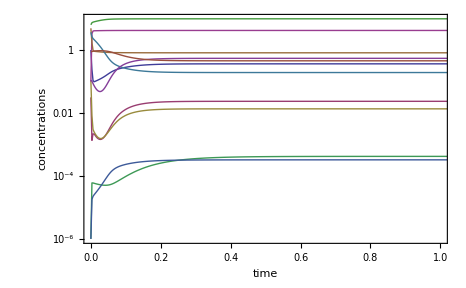

```mathematica
LogPlot[Evaluate[{PYR[t],ACP[t],ACAL[t],ACLAC[t],ACET[t],ATP[t],ADP[t],NAD[t],NADH[t],ACCOA[t],COA[t]}/.tsol],{t,0,10},PlotRange->{{0,1},{0,10}},Frame->True,BaseStyle->{FontFamily->"Gill Sans Light", FontSize->16},FrameLabel->{"time","concentrations"}]
```

Determination of the steady state concentrations of the model using a time simulation as an initial guess

```mathematica
ss=FindRoot[Table[odes[[i]][[2]]==0,{i,1,Length[odes]}]/.rateqs/.parm,Table[{vars[[i]][t],(vars[[i]][t]/.t->10/.tsol)[[1]]},{i,1,Length[vars]}]];
TableForm[ss]
```

PYR[t]→0.364377
ACP[t]→0.0235334
ACAL[t]→0.0135748
ACLAC[t]→0.000420139
ACET[t]→0.000326168
ATP[t]→4.18328
ADP[t]→0.816726
NAD[t]→9.80709
NADH[t]→0.192909
ACCOA[t]→0.545206
COA[t]→0.454794

```mathematica
Jss=rateqs/.parm/.ss;
TableForm[%]
```

vGLYC→165.783
vLDH→321.232
vPDH→10.3251
vPTA→8.93907
vACK→8.93907
vACALDH→1.38606
vADH→1.38606
vALS→0.0044534
vALDC→0.00445328
vACETEFF→0.0130459
vACETDH→-0.00859245
vATPASE→340.505
vNOX→17.8956
vNEALC→1.26042×10^-7